```mathematica
dp[ n_, k_, c_ ] := Sum[ c^-1 dp[ c n / j, k-1, c],{j,1+c, Floor[n c^k]}];dp[n_,0,c_]:=1
dpa[ n_, k_, c_ ] := Sum[ c^-1 dp[ Floor[c n / j], k-1, c],{j,1+c, Floor[n c^k]}];dp[n_,0,c_]:=1
dp2[ n_, k_, c_ ] := Sum[ dp2[ Floor[n / j], k-1, c],{j,c, n}];dp2[n_,0,c_]:=1
dp2a[n_, k_, c_] := c^-k dp2[ n c^k,k,c+1]
```

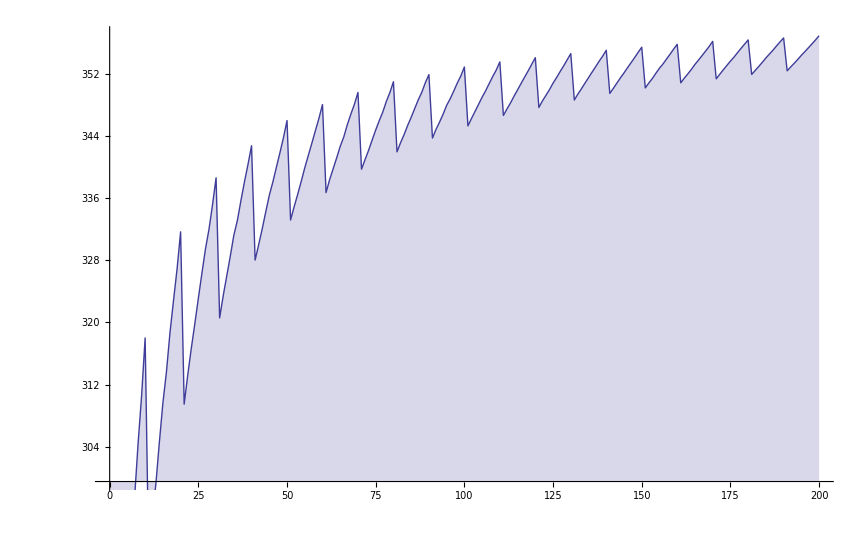

```mathematica
DiscretePlot[dp[100,2,1+n/10],{n,0,200}]
```

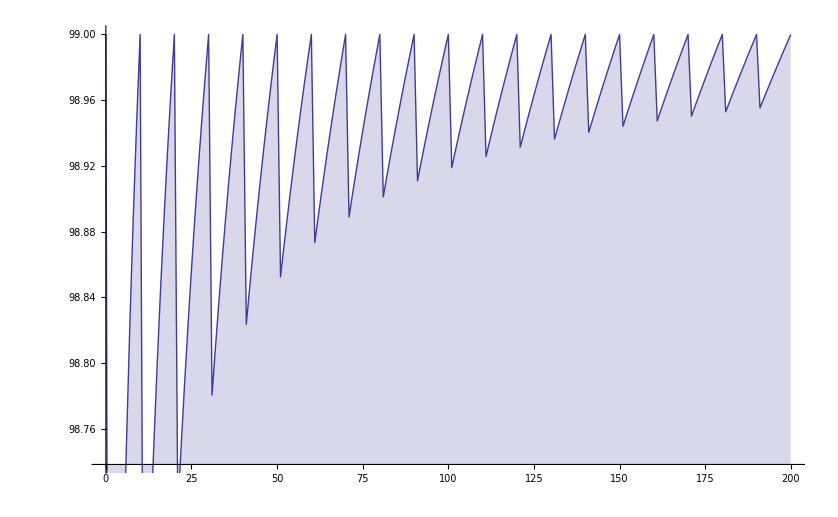

```mathematica
DiscretePlot[dpa[100,1,1+n/10],{n,0,200}]
```

```mathematica
DiscretePlot[dp[100,3,1+n/10],{n,0,200}]
```

$Aborted

```mathematica
3^2dp[100 3^-2,2,3]
```

125

```mathematica
Dhyp[n_,k_,a_]:=Sum[Binomial[k,j] Dhyp[n/(m^(k-j)),j,m+1],{m,a,n^(1/k)},{j,0,k-1}]
Dhyp[n_,1,a_]:=Floor[n]-a+1;Dhyp[n_,0,a_]:=1
```

```mathematica
Dhyp[100,2,4]
```

125

```mathematica
N[dp[100,3,1]]
```

324.

```mathematica
(-1)^(2+1)N[Gamma[2,-Log[100]]/Gamma[2]]
```

360.517-4.41506×10^-14 ⅈ

General::ivar: 3.5 is not a valid variable.

```mathematica
{N[dp[100,2,2+1/10000000]],N[dp[100,2,3]]}
```

{285.25,331.667}

```mathematica
{N[dp[100,2,3+1/10000000]],N[dp[100,2,4]]}
```

{307.,338.625}

```mathematica
{N[dp[100,2,4+1/10000000]],N[dp[100,2,5]]}
```

{318.875,342.76}

```mathematica
{N[dp[100,2,5+1/10000000]],N[dp[100,2,6]]}
```

{326.32,346.}

```mathematica
Table[{a,N[dp[100,1,a+1/10000000]],N[dp[100,1,a]],N[dp[100,1,a]]-N[dp[100,1,a+1/10000000]]},{a,1,10}]//TableForm
```

1 | 98. | 99. | 1.00001
2 | 98.5 | 99. | 0.500005
3 | 98.6667 | 99. | 0.333337
4 | 98.75 | 99. | 0.250002
5 | 98.8 | 99. | 0.200002
6 | 98.8333 | 99. | 0.166668
7 | 98.8571 | 99. | 0.142859
8 | 98.875 | 99. | 0.125001
9 | 98.8889 | 99. | 0.111112
10 | 98.9 | 99. | 0.100001

```mathematica
Table[{a,N[dp[100,2,a+1/10000000]],N[dp[100,2,a]],N[dp[100,2,a]]-N[dp[100,2,a+1/10000000]]},{a,1,10}]//TableForm
```

1 | 234. | 283. | 49.
2 | 285.25 | 318. | 32.75
3 | 307. | 331.667 | 24.6667
4 | 318.875 | 338.625 | 19.75
5 | 326.32 | 342.76 | 16.44
6 | 331.889 | 346. | 14.1111
7 | 335.714 | 348.061 | 12.3469
8 | 338.641 | 349.625 | 10.9844
9 | 341.111 | 351. | 9.8889
10 | 342.93 | 351.92 | 8.99001

```mathematica
Table[{a,N[dp[100,2,a+1/10000000]],N[dp[100,2,a+1]],N[dp[100,2,a+1]]-N[dp[100,2,a+1/10000000]]},{a,1,10}]//TableForm
```

1 | 234. | 318. | 84.
2 | 285.25 | 331.667 | 46.4167
3 | 307. | 338.625 | 31.625
4 | 318.875 | 342.76 | 23.885
5 | 326.32 | 346. | 19.68
6 | 331.889 | 348.061 | 16.1723
7 | 335.714 | 349.625 | 13.9107
8 | 338.641 | 351. | 12.3594
9 | 341.111 | 351.92 | 10.8089
10 | 342.93 | 352.901 | 9.97083

```mathematica
N[dp2a[100,2,2-1/100000000]]
```

315.25

```mathematica
N[dp2a[100-1/1000000,2,2]]
```

315.25

```mathematica
dp[100,3,6.7]
```

608.303

```mathematica
ddp[n_,k_, b_] := N[(dp[n,k,Floor[b]+1/1000000]*(1-(b-Floor[b]))+(b-Floor[b])*dp[n,k,b+1])]
```

```mathematica
6.5-Floor[6.5]
```

0.5

```mathematica
ddp[100,3,6.7]
```

603.821